## RK Code

RK Schemes are going to be specified by Extended Butcher Tables of the form
	c | A
  | b_H
b_L 
where A is a strictly lower triangular matrix of substep weights, c is the vector of inner substep lengths, b_H is the vector pf high precision final slope weights, and b_Lis the vector of low precision final slope weights.

We want to make a general RK individual step procedure and a general step control mechanism.  We are going to mimic the input and output of our development Bogacki-Shampine code.

```mathematica
BSTable=Association[{
"A"->({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 3/4, 0, 0}, {2/9, 1/3, 4/9, 0}}),
"bH"->{2/9,1/3,4/9,0},"orderH"->3,
"bL"->{7/24,1/4,1/3,1/8},"orderL"->3,
"c"->{0,1/2,3/4,1}
}]
```

<|A→{{0,0,0,0},{1/2,0,0,0},{0,3/4,0,0},{2/9,1/3,4/9,0}},bH→{2/9,1/3,4/9,0},orderH→3,bL→{7/24,1/4,1/3,1/8},orderL→3,c→{0,1/2,3/4,1}|>

```mathematica
RKStep[f_,BT_][{h_,t0_,y0_}]:= Module[
{A,bH,bL,c,p,s,z,K},
(* Extract Data from Association *)
{A,bH,bL,c,p}=Map[BSTable,{"A","bH","bL","c","orderL"}];
s=Length[A];
(* Assign space for and compute internal slopes *)
K=ConstantArray[0.0,{Length[y0],s}];
Do[
z=y0+Sum[A⟦i,j⟧ K⟦All,j⟧,{j,1,i-1}];
K⟦All,i⟧=f[t0+c⟦i⟧h,z],
{i,1,s}]; 
(* Compute and return potential updated t, yH, and yL *)
{t0+h, y0+h*Sum[bH⟦i⟧K⟦All,i⟧,{i,1,s}],y0+h*Sum[bL⟦i⟧K⟦All,i⟧,{i,1,s}]}
]
```

```mathematica
BSTable["A"]
```

{{0,0,0,0},{1/2,0,0,0},{0,3/4,0,0},{2/9,1/3,4/9,0}}

```mathematica
LV[{α_,β_,γ_,δ_}][t_,{x_,y_}]:= {α x - β x y, -γ y + δ x y}
params={0.1,0.2,0.3,0.4}; TMax=50.4; t0=0.1;y0={0.1,0.2};
ySol=NDSolveValue[{
y'[t]==LV[params][t,y[t]],
y[t0]==y0},y,{t, t0, TMax}];
ParametricPlot[ySol[t],{t, t0, TMax},
PlotRange->All];
(* Check RK Step Runs *)
h0=0.3;
RKStep[LV[params],BSTable][{h0,t0,y0}]
(* Check RK Runs Correctly *)
```

{0.4,{0.102006,0.186312},{0.102006,0.186295}}

```mathematica
hs=Table[0.5^p,{p,0,12}]
Table[
Map[Norm,RKStep[LV[params],BSTable][{h,t0,y0}]⟦{2,3}⟧-ySol[t0+h]],
{h, hs}]
```

{1.,0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195313,0.000976563,0.000488281,0.000244141}

{{0.0476838,0.0477218},{0.0740138,0.0723451},{0.0870501,0.0857636},{0.0935359,0.0927747},{0.0967707,0.0963599},{0.098386,0.098173},{0.0991932,0.0990848},{0.0995966,0.099542},{0.0997983,0.0997709},{0.0998992,0.0998854},{0.0999496,0.0999427},{0.0999748,0.0999713},{0.0999874,0.0999857}}

```mathematica
{{1.1,{0.10668817390966934,0.15437447884732802},{0.10668798432496092,0.15431531274104512}},{0.6,{0.10334408695483467,0.17718723942366402},{0.10334399216248046,0.17715765637052255}},{0.35,{0.10167204347741735,0.188593619711832},{0.10167199608124024,0.18857882818526128}},{0.225,{0.10083602173870868,0.19429680985591602},{0.10083599804062011,0.19428941409263065}},{0.1625,{0.10041801086935434,0.19714840492795802},{0.10041799902031007,0.19714470704631534}},{0.13125,{0.10020900543467717,0.198574202463979},{0.10020899951015504,0.19857235352315766}},{0.115625,{0.10010450271733859,0.1992871012319895},{0.10010449975507751,0.19928617676157884}},{0.1078125,{0.1000522513586693,0.19964355061599476},{0.10005224987753876,0.19964308838078942}},
{0.10390625,{0.10002612567933465,0.19982177530799738},{0.10002612493876939,0.19982154419039472}},{0.101953125,{0.10001306283966732,0.1999108876539987},{0.1000130624693847,0.19991077209519736}},{0.1009765625,{0.10000653141983366,0.19995544382699937},{0.10000653123469234,0.1999553860475987}},{0.10048828125,{0.10000326570991684,0.1999777219134997},{0.10000326561734618,0.19997769302379936}},{0.100244140625,{0.10000163285495842,0.19998886095674984},{0.1000016328086731,0.1999888465118997}}}
```

```mathematica
Table[
RKStep[LV[params],BSTable][{h0,t0,y0}],
{h0, hs}]
```

```mathematica
{0.2,{0.10066881739096693,0.1954374478847328},{0.1006687984324961,0.1954315312741045}}
```

{0.2,{0.100669,0.195437},{0.100669,0.195432}}

## Fancy Ralston Method

### Code

Code for a Fancy-Ralston step is below.   Taken from https://en.wikipedia.org/wiki/Bogacki%E2%80%93Shampine_method

```mathematica
FancyRalstonStep[f_,h_][{t0_,y0_}]:= Module[
{k1,k2,k3,k4,z1,z2,z3,w},
k1=f[t0,y0];
z1 = y0+1/2 * k1*h; 
k2 = f[t0+1/2 h, z1];
z2= y0 + 3/4*k2*h;
k3=f[t0+3/4 h, z2];
z3=y0 + h*(2/9 k1+1/3 k2 + 4/9 k3);
k4=f[t0+h,z3];
w=y0+h*(7/24 k1 + 1/4 k2 + 1/3 k3 + 1/8 k4);
{t0+h, w,z3}
]
```

### Synthetic ODE

Generate a “synthetic” ODE with a known solution

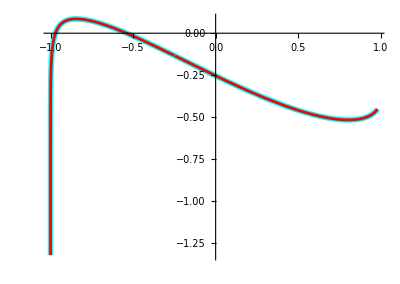

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Sin[t + Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2  +Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
f[t,{y1,y2}];
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ParametricPlot[{ySol[t],SynSol[t]},{t, t0, t0+TMax},
PlotStyle->{{Cyan, Thickness[0.01]},{Red,Thickness[0.005]}}]
```

### Error Behavior

Lets look at the single steps we generate from the Fancy-Ralston (FR) procedure as a function of h.  One of the methods is much more accurate than the other! One is order 3 and the other is order 2.

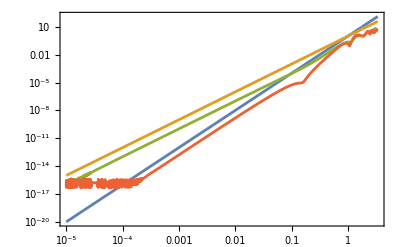

```mathematica
LogLogPlot[ {h^4,h^3,
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦2⟧-SynSol[t0+h]],
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦3⟧-SynSol[t0+h]]
},{h,10^-5,TMax},
GridLines->Automatic,Frame->True]
```

We know what it does!  We need to work out why the two pieces of information are useful.
We know when h is small that 
	||y[t0+h]-z||≈C_1 h^4 and ||y[t0+h]-w||≈C_2 h^3
so 
	||w-z||=||w-y[t0+h]+y[t0+h]-z||≤||w-y[t0+h]||+||y[t0+h]-z||
and
	||w-z||≤C_1 h^4+C_2 h^3≈C_2 h^3.
In words, the computable difference between the two predictions in FR scales like h^3 and provides an estimate for the error of the less accurate prediction w.

### Step Length Prediction

In practice, we want to make sure that our errors at each step are less than some tolerance. A typical tolerance is Tol=10^-7.

After an FR step of size h the error ||y-w||=err≈C_2 h^3.  If err>Tol then h was too large and it makes sense to try again with a scaled step γ h.   The expected error with a scaled step γ h is 
	(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3
If all the estimates were exact the tolerance would be hit if   
	Tol=(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3.
The step size control follows from 
	γ=(Tol/err)^(1/3) 
In practice the more cautious scheme 
	γ=(0.9Tol/err)^(1/3) 
is implemented that tries to satisfy
	0.9 Tol=err γ^3.

When||y-w||=err>Tol the step is bad: skip the update and try again with the smaller step size γ h where γ=(0.9Tol/err)^(1/3)<1.

When||y-w||=err≤Tol the step is good: take the best update z and try the next step with the adjusted step size γ h where γ=(0.9Tol/err)^(1/3)>1.

### Bogaki-Shampine ODE23

The Bogaki-Shampine pair is simply the code in FR with step-size control based on the above.

```mathematica
BogakiShampineStep[f_,Tol_][{t_,y_,h_}]:= Module[{tNew,w,z,err,γ},
{tNew,w,z}=FancyRalstonStep[f,h][{t,y}];
err=Norm[w-z];
γ=(0.9Tol/err)^(1/3);
If[ err≥Tol,
{t,y,γ h},
{tNew,z,γ h}]
]
```

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ODESteps=50;
{Tol,h0}={10^-5,0.1};
Data=NestList[BogakiShampineStep[f,Tol],{t0,y0,h0},ODESteps];
TabView[{
"Sol"->ParametricPlot[ySol[t],{t,t0, TMax},
Epilog->Point[Data⟦All,2⟧]],
"StepSize"->ListLogPlot[Data⟦All,3⟧,
PlotRange->All,
GridLines->Automatic,
Frame->True,
FrameLabel->{"i","h"}]
}
]
```

12